```mathematica
Data={5408,5431,5475,5442,5376,5388,5459,5422,5416,5435,5420,5429,5401,5446,5487,5416,5382,5357,5388,5457,5407,5469,5416,5377,5454,5375,5409,5459,5445,5429,5463,5408,5481,5453,5422,5354,5421,5406,5444,5466,5399,5391,5477,5447,5329,5473,5423,5441,5412,5384,5445,5436,5454,5453,5428,5418,5465,5427,5421,5396,5381,5425,5388,5388,5378,5481,5387,5440,5482,5406,5401,5411,5399,5431,5440,5413,5406,5342,5452,5420,5458,5485,5431,5416,5431,5390,5399,5435,5387,5462,5383,5401,5407,5385,5440,5422,5448,5366,5430,5418}
```

{5408,5431,5475,5442,5376,5388,5459,5422,5416,5435,5420,5429,5401,5446,5487,5416,5382,5357,5388,5457,5407,5469,5416,5377,5454,5375,5409,5459,5445,5429,5463,5408,5481,5453,5422,5354,5421,5406,5444,5466,5399,5391,5477,5447,5329,5473,5423,5441,5412,5384,5445,5436,5454,5453,5428,5418,5465,5427,5421,5396,5381,5425,5388,5388,5378,5481,5387,5440,5482,5406,5401,5411,5399,5431,5440,5413,5406,5342,5452,5420,5458,5485,5431,5416,5431,5390,5399,5435,5387,5462,5383,5401,5407,5385,5440,5422,5448,5366,5430,5418}

```mathematica
Needs["StatisticalPlots`"]
StemLeafPlot[Floor[Data,1],IncludeEmptyStems->True,StemExponent->1]
```

Stem | Leaves
532 | 9
533 | 
534 | 2
535 | 47
536 | 6
537 | 5678
538 | 12345778888
539 | 016999
540 | 11166677889
541 | 123666688
542 | 0011222357899
543 | 01111556
544 | 00012455678
545 | 233447899
546 | 23569
547 | 357
548 | 11257
Stem units: 10

```mathematica
Data={5408,5431,5475,5442,5376,5388,5459,5422,5416,5435,5420,5429,5401,5446,5487,5416,5382,5357,5388,5457,5407,5469,5416,5377,5454,5375,5409,5459,5445,5429,5463,5408,5481,5453,5422,5354,5421,5406,5444,5466,5399,5391,5477,5447,5329,5473,5423,5441,5412,5384,5445,5436,5454,5453,5428,5418,5465,5427,5421,5396,5381,5425,5388,5388,5378,5481,5387,5440,5482,5406,5401,5411,5399,5431,5440,5413,5406,5342,5452,5420,5458,5485,5431,5416,5431,5390,5399,5435,5387,5462,5383,5401,5407,5385,5440,5422,5448,5366,5430,5418,5350}
```

```mathematica
{5408,5431,5475,5442,5376,5388,5459,5422,5416,5435,5420,5429,5401,5446,5487,5416,5382,5357,5388,5457,5407,5469,5416,5377,5454,5375,5409,5459,5445,5429,5463,5408,5481,5453,5422,5354,5421,5406,5444,5466,5399,5391,5477,5447,5329,5473,5423,5441,5412,5384,5445,5436,5454,5453,5428,5418,5465,5427,5421,5396,5381,5425,5388,5388,5378,5481,5387,5440,5482,5406,5401,5411,5399,5431,5440,5413,5406,5342,5452,5420,5458,5485,5431,5416,5431,5390,5399,5435,5387,5462,5383,5401,5407,5385,5440,5422,5448,5366,5430,5418}
```

{5408,5431,5475,5442,5376,5388,5459,5422,5416,5435,5420,5429,5401,5446,5487,5416,5382,5357,5388,5457,5407,5469,5416,5377,5454,5375,5409,5459,5445,5429,5463,5408,5481,5453,5422,5354,5421,5406,5444,5466,5399,5391,5477,5447,5329,5473,5423,5441,5412,5384,5445,5436,5454,5453,5428,5418,5465,5427,5421,5396,5381,5425,5388,5388,5378,5481,5387,5440,5482,5406,5401,5411,5399,5431,5440,5413,5406,5342,5452,5420,5458,5485,5431,5416,5431,5390,5399,5435,5387,5462,5383,5401,5407,5385,5440,5422,5448,5366,5430,5418}

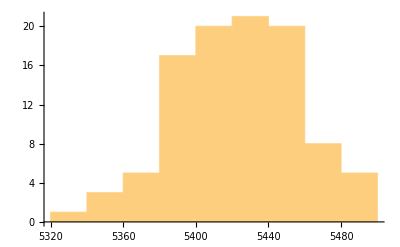

```mathematica
Histogram[Data]
```

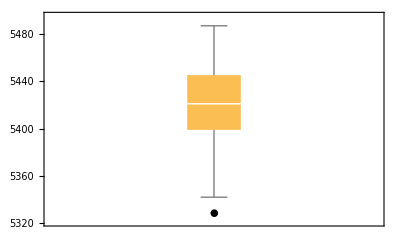

```mathematica
BoxWhiskerChart[Data,{{"Outliers"}}]
```